# Extract Data From Discrete Plot Images Using Semantic Segmentation (Pixel Classification)

Wangping Ren

Jofre Espigule-Pons

## Introduction

Discrete plots are one of the charts that are used widely in almost all fields of science, business and industry for the purpose of data virtualization. It is often of great interest to extract the numerical values of the data from discrete plots in the form of images for further analyzing and processing, such as the analysis of discrete data images from scientific papers. However, most data extraction software requires manual data extraction and axes establishment from the user which is time-consuming. In this project, we present an automated data extraction system for discrete plot images that utilizes a semantic segmentation approach where image pixels are classified as being different parts of the image by using a neural network model called Dilated ResNet-22.

## Methods

The project consists of three parts: generating training and testing data, pixel classification and data extraction. To achieve as much diversity as possible for the training data, we randomize the axes ranges and scales, data point colors and data point shapes for a large amount of data. We then use a semantic segmentation approach to identify and classify pixels in an image that correspond to four distinct parts of it: background, axes, axes labels and data points. Finally, we use an imaging processing approach to extract numerical coordinates of the data from discrete plot images.

## Training and testing data generation

Below is the code that generates a set of training and testing data with a diverse range of color, axes ranges and data point shapes with plot images as inputs and tensor representation as outputs. For the neural network training, 900 discrete training plots and 100 testing plots were used.

```mathematica
theme = "Monochrome"; (* or default *)

(* generating ranges for x and y axes *)
ranges[ max_Integer, di_Integer ] := Flatten[Table[ { { -100 + i, 0 + i }, { -100 + j, 0 + j } },{ i, 0, 100, 10 },{ j, 0, max, di } ], 1 ]


(* generating random 2D points with five different colors for the plots *)
getRandomPointsList[ nPoints_Integer, ranges_ ] := ParallelMap[ Partition[ Transpose@{ RandomReal[ First[ # ], nPoints ], RandomReal[ Last[ # ], nPoints ] }, Round[ nPoints/5]]&, ranges ]


(* generating corresponding scattered plot images *)
getRasterizedPlots[ data_, ranges_ ] := ParallelMap[ Rasterize[ ListPlot[ First[ # ], PlotRange -> Last[ # ],PlotTheme -> theme ], ImageSize -> { 360, 240} ] &, Transpose[ { data, ranges } ] ]


(* extracting raw axes from scattered plots *)
getRawAxes[ data_, ranges_ ] := ParallelMap[ 
                                 AlphaChannel[ 
                                  Rasterize[ 
                                   ListPlot[ First[ # ], PlotRange -> Last[ # ], PlotStyle -> Transparent, LabelStyle -> Transparent, BaseStyle -> { Antialiasing -> False }, PlotTheme -> theme ],
                                  Background -> None, ImageSize -> { 360, 240 } ] ]&,
                                  Transpose[ { data, ranges} ] 
                                  ]

(* extracting raw labels from scattered plots *)
getRawLabels[data_,axes_,ranges_] := MapThread[
                                      ImageDifference[
                                       Binarize[
                                        AlphaChannel[
                                         Rasterize[
                                          ListPlot[#1, PlotRange-> #3, PlotStyle->Transparent, BaseStyle->{Antialiasing->False},PlotTheme->theme], 
                                           Background->None, ImageSize->{360,240}]],
                                       0],#2]&,
                                     {data, axes, ranges}
                                      ]

(* generating binarized points from scattered plots *)
getBinarizedPoints[data_,ranges_]:= ParallelMap[
                                     AlphaChannel[
                                      Rasterize[
                                       ListPlot[First[#], PlotRange->Last[#], AxesStyle->Transparent, BaseStyle->{Antialiasing->False},PlotTheme->theme],
                                      Background->None, ImageSize->{360,240}]]&, 
                                    Transpose[{data,ranges}]
                                     ]
                                     
(* filtering out points that are overlapping with the axes and axes labels *)
getAxes[axes_, binarizedPoints_]:= MapThread[ImageSubtract[#1, #2]&,{axes, binarizedPoints}]
getLabels[binarizedPoints_, labels_]:= MapThread[ImageSubtract[#1, #2]&,{labels, binarizedPoints}]

(* generating backgrounds from scattered plots *)
getBackgrounds[axes_,labels_,binarizedPoints_]:= MapThread[ColorNegate[ImageAdd[#1,#2,#3]]&,{axes,labels,binarizedPoints}]


(* generating image segmentations from scattered plots with four classes where background, axes, axes labels and data points are labeled as 1, 2, 3, 4 respectively *)
segmentateImage[background_,axes_,labels_,binarizedPoints_]:= Round[ImageData[ImageAdd@@MapThread[ImageMultiply,{Image[{background, axes, labels, binarizedPoints},"Real32"],{1,2,3,4}}]]]

getSegmentations[dataPoints_,ranges_]:=Module[{r=ranges,data=dataPoints, binarizedPoints, axes, labels, backgrounds},
binarizedPoints=getBinarizedPoints[data,r];
axes=getAxes[getRawAxes[data,r], binarizedPoints];
labels=getLabels[binarizedPoints, getRawLabels[data, axes,r]];
backgrounds=getBackgrounds[axes, labels, binarizedPoints];
MapThread[segmentateImage[#1, #2, #3, #4]&,{backgrounds, axes, labels, binarizedPoints}]
]
```

```mathematica
(* generating training data where scattered plots are used as inputs and image segmentation is used as outputs for the NetTrain function *)
createTrainingData[ max_, di_, nPoints_Integer ] := Module[{ranges=ranges[max,di], data, plotsImages, segmentations},
data = getRandomPointsList[ nPoints, ranges ];
plotsImages = getRasterizedPlots[ data, ranges ];
segmentations = getSegmentations[ data, ranges ];
MapThread[ Rule[ #1, #2 ]&, { plotsImages, segmentations } ]
]
```

```mathematica
(* create a dataset with "default" theme *)
defaultThemePlots = Flatten@Table[ createTrainingData[ 100, 10, 50 ], 5 ];

(* create a dataset with "monochrome" theme *)
monochromeThemePlots = Flatten@Table[createTrainingData[100,10,50],5];

(* create a mixed dataset with both "default" and "monochrome" themes by joining the above datasets *)
SeedRandom[1234];
data = RandomSample[ Join[ monochromeThemePlots, defaultThemePlots ] ];
```

```mathematica
(* set working directory *)
SetDirectory[NotebookDirectory[]]

(* export generated data to working directory *)
Export["data_diversified.wl",data]

(* create training and testing dataset *)
trainingSet=Take[data,1100];
testSet=Take[data,-110];
```

## Neural network model import, modification and training

We imported an image segmentation model ResNet-22 trained on Cityscapes Data which is ideally suited for the pixel classification of discrete plot images. We classify any input discrete plot image as four distinct classes: backgrounds, axes, labels and data points, which are labeled as “1”, “2”, “3” and “4” respectively. The ResNet-22 neural net output is then represented by a tensor composed by the labeled four classes.

```mathematica
(* import the ResNet-22 neural network from the Wolfram Neural Net Repository *)
net = NetModel[ "Dilated ResNet-22 Trained on Cityscapes Data"]
```

NetGraph[<>]

```mathematica
(* modify the ResNet-22 neural network to meet the input needs *)
ourNet = NetReplacePart[ net, {"input_0" -> NetEncoder[ { "Image" , { 360, 240 } } ], "Output" -> NetDecoder[ { "Class", Range[ 1,19 ], "InputDepth" -> 3 } ] } ];
```

```mathematica
(* train the modified neural network with generated training set using GPU *)
trainedNet = NetTrain[ ourNet, <|"input_0" -> First/@trainingSet, "Output" -> Last/@trainingSet|>, LossFunction -> CrossEntropyLossLayer[ "Index" ], TargetDevice -> " GPU " ]
```

NetGraph[<>]

```mathematica
(* export trained neural network to local directory *)
Export["trained_net.wlnet",trainedNet]
```

```mathematica
(* import trained neural network *)
trainedNet = Import[ "trained_net.wlnet" ]
```

NetGraph[<>]

Testing the trained neural network with one of the generated training plots:

```mathematica
input0= -Graphics-;
```

```mathematica
(* apply the trained neural network to the above input plot *)
trainedNet[ImageResize[input0, {360, 240}]] // Colorize
```

-Graphics-

As shown above, the trained and modified ResNet-22 was able to identify the discrete image plot by recognizing axes, axes labels, backgrounds and data points:

```mathematica
(* define m as the neural network output tensor *)
m = trainedNet[ImageResize[input0, {360, 240}]];
```

```mathematica
(* get image segmentations *)
{pointsData, imageLabels, imageBackground, imageAxes} = {m/.{1->0,2->0,3->0}//Colorize, m/.{1->0,2->0,4->0}//Colorize, m/.{4->0,2->0,3->0}//Colorize, m/.{1->0,4->0,3->0}//Colorize}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Data extraction using image processing

After successfully classifying pixels and segmenting them into four classes, we are now in a good position to extract numerical values from the plot images.

### Get pixel positions for data points

```mathematica
(* get pixel positions for the centers of data points *)
points = ComponentMeasurements[pointsData, "Centroid"][[All, 2]]
HighlightImage[pointsData,points]
```

{1→{336.,230.7},2→{266.214,228.},3→{159.136,226.955},4→{22.6,216.25},5→{164.885,218.115},6→{115.,205.},7→{302.,202.},8→{242.8,199.8},9→{64.8846,195.115},10→{137.1,191.567},11→{17.,191.7},12→{139.1,184.9},13→{51.6667,180.917},14→{7.25,176.167},15→{32.75,175.833},16→{190.75,173.417},17→{340.,173.},18→{216.885,163.885},19→{327.,148.},20→{286.,132.},21→{254.811,126.967},22→{19.,128.},23→{264.955,124.227},24→{260.5,122.5},25→{259.,120.5},26→{147.,116.},27→{188.,111.},28→{84.,105.},29→{110.,99.},30→{131.,98.},31→{224.,95.},32→{88.,94.},33→{16.,85.},34→{181.,84.},35→{89.,78.},36→{123.,77.},37→{107.,75.},38→{332.,72.},39→{140.115,66.1154},40→{160.,65.},41→{150.731,61.7308},42→{91.,54.},43→{61.,51.},44→{162.,45.},45→{240.967,42.6333},46→{251.,39.},47→{103.885,36.8846},48→{245.038,29.8077},49→{137.,16.}}

-Graphics-

### Get axes scale and the origin

```mathematica
(* identify horizontal and vertical axes *)
lines = ImageLines[imageAxes, 0.2,MaxFeatures->2];
{xAxis,yAxis}=lines;
HighlightImage[input0, lines]
```

-Graphics-

```mathematica
(* identify horizontal axes scales by treating them as image corners *)
dotOnX=SortBy[Select[ImageCorners[imageAxes, Method->"HarmonicMean"], RegionDistance[xAxis, #]<3 &],First];
HighlightImage[input0, dotOnX]

(* identify vertical axes scales by treating them as image corners *)
dotOnY=SortBy[Select[ImageCorners[imageAxes, Method->"HarmonicMean"], RegionDistance[yAxis, #]<3 &], Last];
HighlightImage[input0, dotOnY]
```

-Graphics-

-Graphics-

```mathematica
(* get vertical axis sclae by averaging the distances between ajacent corner points as shown above *)
ySteps=Sort[Differences[Last /@ dotOnY]];
ySteps=Drop[ySteps, FirstPosition[ySteps,Max[ySteps]]];
ySteps=Drop[ySteps, FirstPosition[ySteps,Max[ySteps]]];
ySteps=Drop[ySteps, FirstPosition[ySteps,Min[ySteps]]];
ySteps=Drop[ySteps, FirstPosition[ySteps,Min[ySteps]]];
yStep = Mean[ySteps]

(* get honrizontal axis sclae by averaging the distances between ajacent corner points as shown above *)
xSteps=Sort[Differences[First /@ dotOnX]];
xSteps=Drop[xSteps, FirstPosition[xSteps,Max[xSteps]]];
xSteps=Drop[xSteps, FirstPosition[xSteps,Min[xSteps]]];
xSteps=Drop[xSteps, FirstPosition[xSteps,Max[xSteps]]];
xSteps=Drop[xSteps, FirstPosition[xSteps,Min[xSteps]]];
xStep = Mean[xSteps]
```

10.0556

17.4706

```mathematica
(* get pixel position for the intersection between horizontal and vertical axes or the origin *)
originPoint = RegionIntersection[xAxis,yAxis]
```

Point[{{251.326,186.102}}]

### Recover numerical data points

At this point, we have the information about axes scales, pixel positions of each data points and the origin, the only component left to convert pixel positions to coordinates in the Cartesian system is the numerical values of labels. We plan to implement a second neural network as optical character recognition (OCR) to identify axes label values. Due to limited time of the project, we extracted the label information manually.

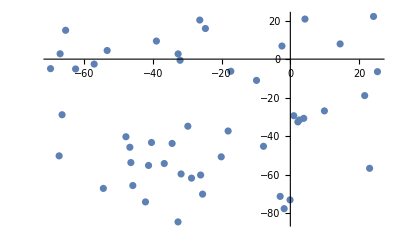

```mathematica
(* convert pixel positions to coordinates in Cartesian system *)
listCoordinates = Function[p, {( First[p] - originPoint[ [1, 1, 1] ] )/xStep/4*20, (Last[p] - originPoint[ [1, 1, 2] ])/yStep/4*20}]/@points;

(* recover discrete data points *)
ListPlot[listCoordinates]
```

### Recover data points color

```mathematica
(* label each pixel points in order *)
listPixelCoordinates = MapThread[Rule[#1,#2]&, {Range[49], points}];

(* identify the color for each pixel point by comparing to the original input image *)
listpointsColors = MapIndexed[RGBColor@PixelValue[ originalplot, #1 ] -> First@#2&, Values@listPixelCoordinates]
```

{RGBColor[{0.9254901960784314, 0.3843137254901961, 0.20784313725490197}]→1,RGBColor[{0.5294117647058824, 0.47058823529411764, 0.7019607843137254}]→2,RGBColor[{0.3686274509803922, 0.5058823529411764, 0.7098039215686275}]→3,RGBColor[{0.8588235294117647, 0.9019607843137255, 0.7686274509803922}]→4,RGBColor[{0.8823529411764706, 0.611764705882353, 0.1411764705882353}]→5,RGBColor[{0.5294117647058824, 0.47058823529411764, 0.7019607843137254}]→6,RGBColor[{0.3686274509803922, 0.5058823529411764, 0.7098039215686275}]→7,RGBColor[{0.9254901960784314, 0.3843137254901961, 0.20784313725490197}]→8,RGBColor[{0.9254901960784314, 0.3843137254901961, 0.20784313725490197}]→9,RGBColor[{0.5607843137254902, 0.6941176470588235, 0.19215686274509805}]→10,RGBColor[{0.9372549019607843, 0.4823529411764706, 0.3333333333333333}]→11,RGBColor[{0.3686274509803922, 0.5058823529411764, 0.7098039215686275}]→12,RGBColor[{0.5294117647058824, 0.47058823529411764, 0.7019607843137254}]→13,RGBColor[{0.5294117647058824, 0.47058823529411764, 0.7019607843137254}]→14,RGBColor[{0.9019607843137255, 0.6745098039215687, 0.27450980392156865}]→15,RGBColor[{0.8823529411764706, 0.611764705882353, 0.1411764705882353}]→16,RGBColor[{0.3686274509803922, 0.5058823529411764, 0.7098039215686275}]→17,RGBColor[{0.8823529411764706, 0.611764705882353, 0.1411764705882353}]→18,RGBColor[{0.5294117647058824, 0.47058823529411764, 0.7019607843137254}]→19,RGBColor[{0.5607843137254902, 0.6941176470588235, 0.19215686274509805}]→20,RGBColor[{0.984313725490196, 0.8627450980392157, 0.8274509803921568}]→21,RGBColor[{0.3686274509803922, 0.5058823529411764, 0.7098039215686275}]→22,RGBColor[{0.5294117647058824, 0.47058823529411764, 0.7019607843137254}]→23,RGBColor[{0.8872549019607843, 0.6274509803921569, 0.17450980392156862}]→24,RGBColor[{0.996078431372549, 0.9882352941176471, 0.9725490196078431}]→25,RGBColor[{0.5294117647058824, 0.47058823529411764, 0.7019607843137254}]→26,RGBColor[{0.3686274509803922, 0.5058823529411764, 0.7098039215686275}]→27,RGBColor[{0.9254901960784314, 0.3843137254901961, 0.20784313725490197}]→28,RGBColor[{0.8823529411764706, 0.611764705882353, 0.1411764705882353}]→29,RGBColor[{0.5607843137254902, 0.6941176470588235, 0.19215686274509805}]→30,RGBColor[{0.3686274509803922, 0.5058823529411764, 0.7098039215686275}]→31,RGBColor[{0.5607843137254902, 0.6941176470588235, 0.19215686274509805}]→32,RGBColor[{0.5294117647058824, 0.47058823529411764, 0.7019607843137254}]→33,RGBColor[{0.5607843137254902, 0.6941176470588235, 0.19215686274509805}]→34,RGBColor[{0.8823529411764706, 0.611764705882353, 0.1411764705882353}]→35,RGBColor[{0.5607843137254902, 0.6941176470588235, 0.19215686274509805}]→36,RGBColor[{0.3686274509803922, 0.5058823529411764, 0.7098039215686275}]→37,RGBColor[{0.8823529411764706, 0.611764705882353, 0.1411764705882353}]→38,RGBColor[{0.9254901960784314, 0.3843137254901961, 0.20784313725490197}]→39,RGBColor[{0.5607843137254902, 0.6941176470588235, 0.19215686274509805}]→40,RGBColor[{0.5294117647058824, 0.47058823529411764, 0.7019607843137254}]→41,RGBColor[{0.9254901960784314, 0.3843137254901961, 0.20784313725490197}]→42,RGBColor[{0.5607843137254902, 0.6941176470588235, 0.19215686274509805}]→43,RGBColor[{0.9254901960784314, 0.3843137254901961, 0.20784313725490197}]→44,RGBColor[{0.8823529411764706, 0.611764705882353, 0.1411764705882353}]→45,RGBColor[{0.5607843137254902, 0.6941176470588235, 0.19215686274509805}]→46,RGBColor[{0.8823529411764706, 0.611764705882353, 0.1411764705882353}]→47,RGBColor[{0.5294117647058824, 0.47058823529411764, 0.7019607843137254}]→48,RGBColor[{0.9254901960784314, 0.3843137254901961, 0.20784313725490197}]→49}

```mathematica
(* classify data points by color *)
FindClusters[listpointsColors,6]
```

{{1,8,9,11,28,39,42,44,49},{2,3,6,7,12,13,14,17,19,22,23,26,27,31,33,37,41,48},{4},{5,15,16,18,24,29,35,38,45,47},{10,20,30,32,34,36,40,43,46},{21,25}}

```mathematica
(* Recover data points color *)
result0 = ListPlot@Map[Part[listCoordinates,#]&,FindClusters[listpointsColors,6]]//Rasterize
```

-Graphics-

## Results and analysis

```mathematica
(* Compare input image and interpretation *)
Grid[{{Input, Interpretation},{ImageResize[input0, {360, 240}],ImageResize[result0,{360, 240}]}},Frame -> All, ItemSize->{22, 3}]
```

Input | Interpretation
-Graphics- | -Graphics-

The above pixel classification and image processing approach successfully interpreted data points as numerical values from an image. Though the color identification rate is  low for this case, it could be improved by finding the appropriate numbers of color groups. Furthermore, this method has difficulty identifying points that are clustered closely together or overlapped. As mentioned above, optical character recognition (OCR) can be applied for identifying axes labels to increase the system’s automation level.

## Future work

Though our training data for the ResNet-22 neural network has randomized data points, axes ranges and data shapes, it is not diverse enough. In future work, we plan to include plots of different styles, different rotations, different label styles and so forth. We also plan to implement a second neural network to achieve optical character recognition (OCR) of various label numbers on the plot axes to increase the system’s automation level. Furthermore, we also aim to generalize this approach to a diverse types of discrete plots which may include “marketing”, “detailed”, “classic” and etc.

## Contact information

peterren16@gmail.com